# Operating with the Fresco files

## Setting current directory, file names etc.

```mathematica
frescoExe=If[$OperatingSystem=="Windows","frescoWin.exe"]
```

frescoWin.exe

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\urazbekov\Documents\GitHub\menim_jumys_codym

```mathematica
directoryName="2H13C_15MEV\\SPE_inelastic_channel\\";
If[!DirectoryQ[directoryName],CreateDirectory[directoryName]]
```

```mathematica
FileNames["*.txt",directoryName];
currectFile=%
```

{2H13C_15MEV\SPE_inelastic_channel\2H13C.txt}

## Run fresco

```mathematica
plotFromFile[fileName_,expFile_:"_",plotLabel_:""]:=If[FileExistsQ[fileName],
Module[{importedData,plotData,labelPlot,plot,subLabelPlot,exp,expPlot},
importedData=Import[fileName,"Table"];
plotData=Cases[importedData,{_Real,_Real}];
labelPlot=Cases[importedData,{"@subtitle",__}];
labelPlot=Flatten[Drop[labelPlot,None,1]];
subLabelPlot=Flatten[Cases[importedData,{"#legend",__}]];
labelPlot=StringJoin[labelPlot,"\n",subLabelPlot⟦4⟧];
plot=ListLogPlot[plotData,Joined->True,Frame->True,AspectRatio->1.5,FrameLabel->{"θ_cm, degree","dΩ/dσ, mb/sr"},ImageSize->Medium,PlotLabel->plotLabel];
If[expFile≠ "_",expPlot=ListLogPlot[
Cases[
Import[StringJoin[directoryName,expFile],"Table"]
,{_Real,_Real}]
];

exp=Export[StringJoin[directoryName,StringReplace[fileName,"."->""],".pdf"],Show[plot,expPlot,PlotRange->Automatic],"PDF"];
Show[plot,expPlot,PlotRange->Automatic]
,
exp=Export[StringJoin[directoryName,StringReplace[fileName,"."->""],".pdf"],plot,"PDF"];
plot]
]];
```

```mathematica
StringJoin[frescoExe," < ", currectFile, " > ",StringDrop[currectFile,-4],".out" ]
Run[% ]
```

frescoWin.exe < 2H13C_15MEV\SPE_inelastic_channel\2H13C.txt > 2H13C_15MEV\SPE_inelastic_channel\2H13C.out

0

## Plot and Export calculated Data

```mathematica
expFileNameList={"\\exp\\14.dat","\\exp\\36814.dat","\\exp\\7514.dat","\\exp\\68614.dat"};
csFileNameList={"fort.201","fort.202","fort.203","fort.204"};
```

```mathematica
SetAttributes[plotFromFile,Listable];
```

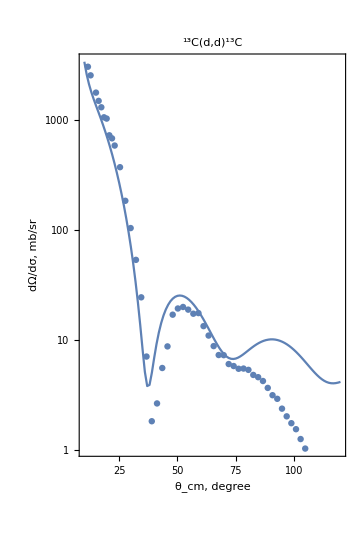

```mathematica
plotFromFile["fort.201","\\exp\\14.dat","^13C(d,d)^13C"]
```

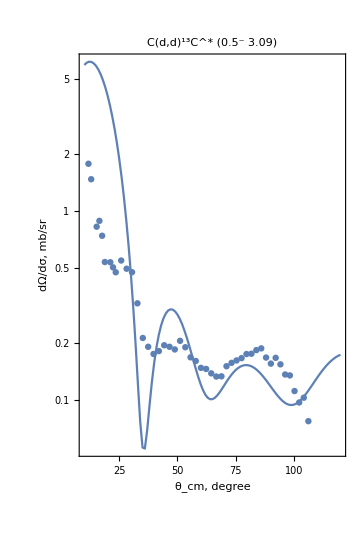

```mathematica
plotFromFile["fort.202","//exp//30914.dat","C(d,d)^13C^* (0.5^- 3.09)"]
```

```mathematica
FilePrint["2H13C_15MEV\\SPE_inelastic_channel\\2H13C.out"]
Run["del fort.*"]
```

FRESCO - FRES 2.9: Coupled Reaction Channels
 Assuming NAMELIST input.

 2H+13C at 14.5 MeV;                                                             

   0.100  60.000   0.500   0.000   0.000   0.000   0.000   0.000   0.000   0.000

 Centre-of-mass Range is    602 * 0.1000 fm., Maximum at  60.00 fm., Interpolating NL forms every  0.50 fm.
 Non - locality width is      4 * 0.1000 fm., Maximum of   0.30 fm., Centred at  0.00 fm.
 2-Nucleon Separation of      0 * 0.5000 fm., Maximum of   0.00 fm., Minimum at  0.00 fm.
 Maximum single particle bins of 60.0000 fm.
               M,Mint =  601 601


 Range of total J is     0.0 <= J <=    30.0 (at least     0.0) and Absorbtion =>     0.0010 mb.
 Dry Run = F, CC set limits =  0  0, Relativistic kinematics =  , Both/Far/Near Analyses =  1

 Cross Sections (and up to T0 for 0=projectile) for Theta from  10.0 to-120.0 in steps of  1.0 degrees.  Coordinates = 0 (Mads)

 Lower Radial Cutoff = maximum of -1.60*L*h &       0.0 fm.,  Lower Cutoff for Couplings =   0.0  fm.


 Iterate Couplings between   0 and   3 times, to  0.000 % if sooner.                                          
  Block solved exactly =   2 chs., with Pade = 0 & Isocen =  =0, NOSOL = F, initwf =  0
  NL quadrature with   18 Gaussian points, Calculate multipoles up to    36 from   0
  M-transfers for lp+lt greater than or equal to  6, Angular Integration Cutoff below  2.7778 %


 Trace switches are :  CHANS =  1, LISTCC =  0, TRENEG =  0, CDETR =  0, SMATS =  2, XSTABL =  1, NLPL =  0

                       WAVES =  0, LAMPL =  0, VEFF =  0, KFUS =  0, WDISK =  0, BPM =  0, MELFIL =  0

                       CDCC =  0, NFUS =  0

 Using unit mass = 1.000000 amu and 1/fine-structure constant = 137.03599 ( 1.000000 * true ) with hc = 197.32705 MeV.fm,
  thus 2*amu/hbar^2 = 0.0478450 = 1/20.9008 and Coulomb constant = 0.1574855 so e^2 = 1.43997, and nuclear magneton= 0.1261183

 Now pre-scan input and save to file 3



 *********** PARTITION NUMBER  1 ******************************************************************************************

   PROJ=d          MASS=  2.0000 Z=   1.0,        # STATES=    2T, TARG=C13      MASS= 13.0000 Z=   6.0,     Q-VALUE =  -0.0000 MEV.

     1:  J= 1.0+ (B# 1), E=  0.0000, K= 0.0              Potl# 11       J= 0.5- (B#-1), E=  0.0000, K= 0.5    

     2:  J= 1.0+ (B# 1), E=  0.0000, K= 0.0              Potl# 11       J= 0.5+ (B# 1), E=  3.0890, K= 0.5    
                                  (Just State  1)


 *********** PARTITION NUMBER  2 ******************************************************************************************

   PROJ=3-H        MASS=  3.0000 Z=   1.0,        # STATES=   -1T, TARG=12-C     MASS= 12.0000 Z=   6.0,     Q-VALUE =   1.3109 MEV.

     1:  J= 0.5+ (B# 1), E=  0.0000, K= 0.5              Potl#  1       J= 0.0+ (B# 1), E=  0.0000, K= 0.0    
0****** WARNING : COMPARED WITH PARTITION  1, THIS PARTITION HAS TOTAL MASS & CHARGE EXCESSES   0.00141 &   0.0000


 ************************************************************************************************************************************

 The following POTENTIALS are defined :

  KP#       TYPE      IT    SHAPE      at     V1        r1        a1        V2        r2        a2        A-in     A-used


                                            A#1       A#2        r0c       ac                                                h @ 2
    1    0=Coulomb       0=CHARGE (WS)  1    13.000     2.000    0.8460    0.0000    0.0000    0.0000     0.000    47.095   0.10000

    1    1=Volume        0=Woods-Saxon  2   86.1390    0.7680    0.7180    0.0000    0.0000    0.0000     0.000    47.095

    1    2=Surface       0=Woods-Saxon  3    0.0000    0.0000    0.0000    3.0000    0.8260    0.9170     0.000    47.095
   --------------------------------------------------------------------------------------------------------------------

                                            A#1       A#2        r0c       ac                                                h @ 0
    2    0=Coulomb       0=CHARGE (WS)  4     0.000    13.000    1.5000    0.0000    0.0000    0.0000     0.000    13.000   0.10000

    2    1=Volume        0=Woods-Saxon  5  102.5000    1.0000    0.8000    2.0000    0.9000    0.6000     0.000    13.000

    2    2=Surface       0=Woods-Saxon  6    0.0000    0.0000    0.0000    2.0400    2.0000    0.6000     0.000    13.000
   --------------------------------------------------------------------------------------------------------------------

                                            A#1       A#2        r0c       ac                                                h @ 1
   11    0=Coulomb       0=CHARGE (WS)  7     2.000    13.000    0.8090    0.0000    0.0000    0.0000     0.000    47.095   0.10000
   --------------------------------------------------------------------------------------------------------------------

                                            A#1       A#2        r0c       ac                                                h @ 0
   12    0=Coulomb       0=CHARGE (WS)  8    12.000     2.000    1.5000    0.0000    0.0000    0.0000     0.000    44.714   0.10000

   12    1=Volume        0=Woods-Saxon  9   96.1390    0.6770    0.8000    0.0000    1.2000    0.5000     0.000    44.714

   12    2=Surface       0=Woods-Saxon 10    0.0000    0.7680    0.7180   41.2450    0.9220    0.5680     0.000    44.714
   --------------------------------------------------------------------------------------------------------------------

                                            A#1       A#2        r0c       ac                                                h @ 0
    8    0=Coulomb       0=CHARGE (WS) 11     2.000     0.000    0.6500    0.0000    0.0000    0.0000     0.000     2.000   0.10000

    8    2=Surface       0=Woods-Saxon 12    5.0000    1.2400    1.2000    8.2450    1.2000    1.2000     0.000     2.000
   --------------------------------------------------------------------------------------------------------------------

                                            A#1       A#2        r0c       ac                                                h @ 0
   14    0=Coulomb       0=CHARGE (WS) 13     0.000    12.000    1.2500    0.0000    0.0000    0.0000     0.000    12.000   0.10000

   14    1=Volume        0=Woods-Saxon 14   39.7780    1.2500    0.6500    0.0000    0.0000    0.0000     0.000    12.000


 ************************************************************************************************************************************

 The following SINGLE-PARTICLE FORM FACTORS are constructed :


 No.   P1 P2 IN KIND T N  L  S1 IA J/S  IB BIND XFER  BE    SC PC FIL AFRAC Adjust  to  Z  Mass   K     Norm    rms      D0     D   ANC/Gsp

 For Channel #  1 with l = 1,  j =  0.5, around core state #  1

   R    Y(R)
   0.00   0.0000E+00,    0.50   6.3071E-02,    1.00   2.2495E-01,    1.50   4.1746E-01,    2.00   5.6503E-01,    2.50   6.2248E-01, 
   3.00   5.9287E-01,    3.50   5.1206E-01,    4.00   4.1728E-01,    4.50   3.3000E-01,    5.00   2.5754E-01,    5.50   2.0006E-01, 
   6.00   1.5531E-01,    6.50   1.2069E-01,    7.00   9.3936E-02,    7.50   7.3231E-02,    8.00   5.7177E-02,    8.50   4.4704E-02, 
   9.00   3.4994E-02,    9.50   2.7422E-02,   10.00   2.1508E-02,   10.50   1.6883E-02,   11.00   1.3262E-02,   11.50   1.0424E-02, 
  12.00   8.1980E-03,   12.50   6.4503E-03,   13.00   5.0774E-03,   13.50   3.9983E-03,   14.00   3.1496E-03,   14.50   2.4819E-03, 
  15.00   1.9563E-03,   15.50   1.5424E-03,   16.00   1.2163E-03,   16.50   9.5941E-04,   17.00   7.5691E-04,   17.50   5.9726E-04, 
  18.00   4.7137E-04,   18.50   3.7207E-04,   19.00   2.9373E-04,   19.50   2.3192E-04,   20.00   1.8313E-04,   20.50   1.4463E-04, 
  21.00   1.1423E-04,   21.50   9.0232E-05,   22.00   7.1282E-05,   22.50   5.6316E-05,   23.00   4.4496E-05,   23.50   3.5160E-05, 
  24.00   2.7785E-05,   24.50   2.1958E-05,   25.00   1.7354E-05,   25.50   1.3716E-05,   26.00   1.0842E-05,   26.50   8.5702E-06, 
  27.00   6.7749E-06,   27.50   5.3559E-06,   28.00   4.2343E-06,   28.50   3.3478E-06,   29.00   2.6469E-06,   29.50   2.0929E-06, 
  30.00   1.6549E-06,   30.50   1.3086E-06,   31.00   1.0348E-06,   31.50   8.1832E-07,   32.00   6.4714E-07,   32.50   5.1179E-07, 
  33.00   4.0476E-07,   33.50   3.2012E-07,   34.00   2.5319E-07,   34.50   2.0025E-07,   35.00   1.5839E-07,   35.50   1.2528E-07, 
  36.00   9.9096E-08,   36.50   7.8385E-08,   37.00   6.2004E-08,   37.50   4.9047E-08,   38.00   3.8798E-08,   38.50   3.0692E-08, 
  39.00   2.4280E-08,   39.50   1.9207E-08,   40.00   1.5195E-08,   40.50   1.2021E-08,   41.00   9.5101E-09,   41.50   7.5238E-09, 
  42.00   5.9524E-09,   42.50   4.7093E-09,   43.00   3.7258E-09,   43.50   2.9478E-09,   44.00   2.3323E-09,   44.50   1.8453E-09, 
  45.00   1.4600E-09,   45.50   1.1552E-09,   46.00   9.1400E-10,   46.50   7.2318E-10,   47.00   5.7221E-10,   47.50   4.5276E-10, 
  48.00   3.5825E-10,   48.50   2.8347E-10,   49.00   2.2430E-10,   49.50   1.7748E-10,   50.00   1.4044E-10,   50.50   1.1113E-10, 
  51.00   8.7935E-11,   51.50   6.9583E-11,   52.00   5.5061E-11,   52.50   4.3571E-11,   53.00   3.4478E-11,   53.50   2.7283E-11, 
  54.00   2.1590E-11,   54.50   1.7085E-11,   55.00   1.3520E-11,   55.50   1.0699E-11,   56.00   8.4665E-12,   56.50   6.7000E-12, 
  57.00   5.3021E-12,   57.50   4.1959E-12,   58.00   3.3205E-12,   58.50   2.6277E-12,   59.00   2.0795E-12,   59.50   1.6457E-12, 
  60.00   1.3023E-12, 

 No.   P1 P2 IN KIND T N  L  S1 IA J/S  IB BIND XFER  BE    SC PC FIL AFRAC Adjust  to  Z  Mass   K     Norm    rms      D0     D   ANC/Gsp

    At R=   59.900, ANC in ch  1 is     1.89752
0   1:  2  1  2  0     1  1 0.5  1 0.5   1  14   0   4.9460  1  1  0 0.7800 VR  1.0000; 0. 1.000 0.4674 1.0000  3.260 -132.9 -185.1  1.8975

 For Channel #  1 with l = 0,  j =  0.5, around core state #  1

   R    Y(R)
   0.00  -0.0000E+00,    0.50   2.6891E-01,    1.00   3.8427E-01,    1.50   2.8614E-01,    2.00   3.7033E-02,    2.50  -2.3288E-01, 
   3.00  -4.2046E-01,    3.50  -5.0113E-01,    4.00  -5.0495E-01,    4.50  -4.6999E-01,    5.00  -4.2119E-01,    5.50  -3.7076E-01, 
   6.00  -3.2364E-01,    6.50  -2.8141E-01,    7.00  -2.4425E-01,    7.50  -2.1182E-01,    8.00  -1.8362E-01,    8.50  -1.5915E-01, 
   9.00  -1.3793E-01,    9.50  -1.1953E-01,   10.00  -1.0359E-01,   10.50  -8.9767E-02,   11.00  -7.7791E-02,   11.50  -6.7413E-02, 
  12.00  -5.8420E-02,   12.50  -5.0626E-02,   13.00  -4.3872E-02,   13.50  -3.8019E-02,   14.00  -3.2947E-02,   14.50  -2.8551E-02, 
  15.00  -2.4742E-02,   15.50  -2.1441E-02,   16.00  -1.8581E-02,   16.50  -1.6102E-02,   17.00  -1.3954E-02,   17.50  -1.2092E-02, 
  18.00  -1.0479E-02,   18.50  -9.0809E-03,   19.00  -7.8694E-03,   19.50  -6.8196E-03,   20.00  -5.9098E-03,   20.50  -5.1213E-03, 
  21.00  -4.4381E-03,   21.50  -3.8460E-03,   22.00  -3.3329E-03,   22.50  -2.8883E-03,   23.00  -2.5029E-03,   23.50  -2.1690E-03, 
  24.00  -1.8796E-03,   24.50  -1.6289E-03,   25.00  -1.4116E-03,   25.50  -1.2233E-03,   26.00  -1.0601E-03,   26.50  -9.1864E-04, 
  27.00  -7.9608E-04,   27.50  -6.8987E-04,   28.00  -5.9784E-04,   28.50  -5.1808E-04,   29.00  -4.4896E-04,   29.50  -3.8907E-04, 
  30.00  -3.3716E-04,   30.50  -2.9218E-04,   31.00  -2.5320E-04,   31.50  -2.1942E-04,   32.00  -1.9015E-04,   32.50  -1.6478E-04, 
  33.00  -1.4280E-04,   33.50  -1.2375E-04,   34.00  -1.0724E-04,   34.50  -9.2930E-05,   35.00  -8.0532E-05,   35.50  -6.9788E-05, 
  36.00  -6.0478E-05,   36.50  -5.2409E-05,   37.00  -4.5417E-05,   37.50  -3.9358E-05,   38.00  -3.4107E-05,   38.50  -2.9557E-05, 
  39.00  -2.5614E-05,   39.50  -2.2197E-05,   40.00  -1.9235E-05,   40.50  -1.6669E-05,   41.00  -1.4445E-05,   41.50  -1.2518E-05, 
  42.00  -1.0848E-05,   42.50  -9.4009E-06,   43.00  -8.1467E-06,   43.50  -7.0598E-06,   44.00  -6.1180E-06,   44.50  -5.3018E-06, 
  45.00  -4.5945E-06,   45.50  -3.9815E-06,   46.00  -3.4503E-06,   46.50  -2.9900E-06,   47.00  -2.5911E-06,   47.50  -2.2454E-06, 
  48.00  -1.9459E-06,   48.50  -1.6863E-06,   49.00  -1.4613E-06,   49.50  -1.2663E-06,   50.00  -1.0974E-06,   50.50  -9.5100E-07, 
  51.00  -8.2413E-07,   51.50  -7.1418E-07,   52.00  -6.1890E-07,   52.50  -5.3633E-07,   53.00  -4.6478E-07,   53.50  -4.0277E-07, 
  54.00  -3.4904E-07,   54.50  -3.0247E-07,   55.00  -2.6212E-07,   55.50  -2.2715E-07,   56.00  -1.9685E-07,   56.50  -1.7058E-07, 
  57.00  -1.4783E-07,   57.50  -1.2811E-07,   58.00  -1.1101E-07,   58.50  -9.6204E-08,   59.00  -8.3369E-08,   59.50  -7.2247E-08, 
  60.00  -6.2608E-08, 

 No.   P1 P2 IN KIND T N  L  S1 IA J/S  IB BIND XFER  BE    SC PC FIL AFRAC Adjust  to  Z  Mass   K     Norm    rms      D0     D   ANC/Gsp

    At R=   59.900, ANC in ch  2 is    -1.81568
0   2:  2  1  2  0     2  0 0.5  1 0.5   2  14   0   1.8570  1  1  0 0.7300 VR  1.4570; 0. 1.000 0.2864 1.0000  4.885  110.0  145.7 -1.8157

 ************************************************************************************************************************************

 TWO-way COUPLING # 1 for partitions  2 <-  1 of KIND  4,   1  0  0 -1 -1 & P1,P2 =    8.0000   1.0000 : for J <=    30.5 & R <  59.7 fm.

      1      1      1      0
      2      1      2      1
      3      2      1      1 tried 
      3      2      1      1
      4      2      2      0
 Using cutoff at     60.0 => NLIM = 120 at  59.5 fm.

     So INELASTIC EXCITATIONS OF SINGLE PARTICLES in the C13      nucleus outside the 12-C     core

     by Q =  1 multipoles of the COUL+NUC parts (0) of V-sp( 8) + V-CC( 1) - V-opt(11) with        FULL  REORIENTATION ( 0)

0Incoming partition  1 in excitation state # 1,   Laboratory Energy given for partition  1 Nucleus 1 in Excitation pair 1

0Lab. ENERGY ranges :

   from    14.5000     to   0.00000     in     0 intervals
   from    0.00000     to   0.00000     in     0 intervals
   from    0.00000     to   0.00000     in     0 intervals

 Largest real,imaginary parts of any form factor at R=   58.90 are   2.44E-02  2.33E-16 MeV
 Finished all Couplings @  0.0468003 18

 Symmetric Hamiltonian
1***********************************************************************************************************************************
************************************************************************************************************************************

        INCOMING d        ;    LABORATORY d        ENERGY =   14.500     MeV.

 ***********************************************************************************************************************************
 ***********************************************************************************************************************************

 Allocate arrays for  5  channels, of which  5  need wfs.

 ######################################################################################################################
 #                                                                                                                    #
 # Total SPIN and PARITY =     0.5 +,    5 channels,    4 in 1st block.  Rmin & Coul turning =    0.0    0.7 fm.  #
 #                                                                                                                    #
 ######################################################################################################################



    C Projectl Target   #   EX.   (L  Proj) J  + Targ = Jtotal     E-cm      Re K     Re Eta     RM*K            CH
    1 d        C13      #    1: I   1 1.0    0.0  0.5     0.5    12.56667   1.02087   0.35093   61.2521  -0.50104  -0.02160 1 1 1   1
    2 d        C13      #    1: I   1 1.0    1.0  0.5     0.5    12.56667   1.02087   0.35093   61.2521  -0.50104  -0.02160 1 1 1   1
    3 d        C13      #    2:     0 1.0    1.0  0.5     0.5     9.47767   0.88656   0.40409   53.1939  -0.37211   0.33683 1 1 1   2
    4 d        C13      #    2:     2 1.0    1.0  0.5     0.5     9.47767   0.88656   0.40409   53.1939   0.49989  -0.04797 1 1 1   2
    5 3-H      12-C     #    1:     0 0.5    0.5  0.0     0.5    13.87757   1.26235   0.39295   75.7412   0.48416  -0.13000 2 1 2   1
   S-matrix    1 =   -0.23769   0.25250 for L=    1, J=    0.0 channel on core I =   0.5 from L=    1,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =   66.635  30.340 deg. for the L =    1, J =    0.0 channel.
       0.5 -0.23769107  0.25249943i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     0.5+/ 1 @ 1 =   8.840 , Out:   0.019/   0.013    0.000#   8.827f

   S-matrix    2 =   -0.23832   0.25175 for L=    1, J=    1.0 channel on core I =   0.5 from L=    1,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =   66.716  30.350 deg. for the L =    1, J =    1.0 channel.
       0.5 -0.23832455  0.25174582i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     0.5+/ 1 @ 2 =   8.841 , Out:   0.019/   0.017    0.000#   8.824f


 Total SPIN, PARITY =     0.5 -,    5 chs,    4 cc.  Rmin & Coul turning =    0.0    0.7
   S-matrix    1 =   -0.31667  -0.08439 for L=    0, J=    1.0 channel on core I =   0.5 from L=    0,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =  -82.539  31.959 deg. for the L =    0, J =    1.0 channel.
       0.5 -0.31667332 -0.08438904i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     0.5-/ 0 @ 1 =   8.969 , Out:   0.000#   0.011    0.000#   8.958f

   S-matrix    2 =    0.09241   0.27721 for L=    2, J=    1.0 channel on core I =   0.5 from L=    2,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =   35.782  35.245 deg. for the L =    2, J =    1.0 channel.
       0.5  0.09241404  0.27721428i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     0.5-/ 2 @ 2 =   9.190 , Out:   0.000#   0.031    0.000#   9.160f

 Allocate arrays for  7  channels, of which  7  need wfs.

 Total SPIN, PARITY =     1.5 +,    7 chs,    6 cc.  Rmin & Coul turning =    0.1    1.8
   S-matrix    1 =   -0.23737   0.25288 for L=    1, J=    1.0 channel on core I =   0.5 from L=    1,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =   66.594  30.336 deg. for the L =    1, J =    1.0 channel.
       1.5 -0.23737433  0.25287624i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     1.5+/ 1 @ 1 =  17.679 , Out:   0.024/   0.022    0.000#  17.657f

   S-matrix    2 =   -0.23864   0.25137 for L=    1, J=    2.0 channel on core I =   0.5 from L=    1,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =   66.756  30.354 deg. for the L =    1, J =    2.0 channel.
       1.5 -0.23864129  0.25136901i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     1.5+/ 1 @ 2 =  17.682 , Out:   0.024/   0.037    0.000#  17.645f

   S-matrix    3 =    0.30941  -0.12958 for L=    3, J=    2.0 channel on core I =   0.5 from L=    3,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =  -11.362  31.291 deg. for the L =    3, J =    2.0 channel.
       1.5  0.30941421 -0.12958012i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     1.5+/ 3 @ 3 =  17.835 , Out:   0.000#   0.057    0.000#  17.778f


 Total SPIN, PARITY =     1.5 -,    7 chs,    6 cc.  Rmin & Coul turning =    0.1    1.8
   S-matrix    1 =   -0.31667  -0.08439 for L=    0, J=    1.0 channel on core I =   0.5 from L=    0,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =  -82.539  31.959 deg. for the L =    0, J =    1.0 channel.
       1.5 -0.31667332 -0.08438904i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     1.5-/ 0 @ 1 =  17.938 , Out:   0.000#   0.023    0.000#  17.915f

   S-matrix    2 =    0.09681   0.27655 for L=    2, J=    1.0 channel on core I =   0.5 from L=    2,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =   35.353  35.167 deg. for the L =    2, J =    1.0 channel.
       1.5  0.09681215  0.27655199i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     1.5-/ 2 @ 2 =  18.371 , Out:   0.044/   0.017    0.000#  18.354f

   S-matrix    3 =    0.09290   0.27714 for L=    2, J=    2.0 channel on core I =   0.5 from L=    2,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =   35.734  35.236 deg. for the L =    2, J =    2.0 channel.
       1.5  0.09290271  0.27714069i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     1.5-/ 2 @ 3 =  18.379 , Out:   0.044/   0.056    0.000#  18.323f


 Total SPIN, PARITY =     2.5 +,    7 chs,    6 cc.  Rmin & Coul turning =    0.3    2.8
   S-matrix    1 =   -0.23706   0.25325 for L=    1, J=    2.0 channel on core I =   0.5 from L=    1,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =   66.554  30.331 deg. for the L =    1, J =    2.0 channel.
       2.5 -0.23705759  0.25325305i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     2.5+/ 1 @ 1 =  26.517 , Out:   0.000#   0.028    0.000#  26.490f

   S-matrix    2 =    0.30652  -0.13493 for L=    3, J=    2.0 channel on core I =   0.5 from L=    3,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =  -11.880  31.338 deg. for the L =    3, J =    2.0 channel.
       2.5  0.30652000 -0.13493065i: elastic S-matrix  @@      0.02  0   0 F  0
 Reaction Xsec     2.5+/ 3 @ 2 =  26.764 , Out:   0.056/   0.062    0.000#  26.702f

   S-matrix    3 =    0.30927  -0.12985 for L=    3, J=    3.0 channel on core I =   0.5 from L=    3,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =  -11.388  31.294 deg. for the L =    3, J =    3.0 channel.
       2.5  0.30926950 -0.12984765i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     2.5+/ 3 @ 3 =  26.753 , Out:   0.056/   0.084    0.000#  26.669f


 Total SPIN, PARITY =     2.5 -,    7 chs,    6 cc.  Rmin & Coul turning =    0.3    2.8
   S-matrix    1 =    0.09698   0.27653 for L=    2, J=    2.0 channel on core I =   0.5 from L=    2,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =   35.337  35.164 deg. for the L =    2, J =    2.0 channel.
       2.5  0.09697504  0.27652746i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     2.5-/ 2 @ 1 =  27.556 , Out:   0.046/   0.024    0.000#  27.532f

   S-matrix    2 =    0.09274   0.27717 for L=    2, J=    3.0 channel on core I =   0.5 from L=    2,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =   35.750  35.239 deg. for the L =    2, J =    3.0 channel.
       2.5  0.09273982  0.27716522i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     2.5-/ 2 @ 2 =  27.570 , Out:   0.046/   0.087    0.000#  27.483f

   S-matrix    3 =    0.00105  -0.06329 for L=    4, J=    3.0 channel on core I =   0.5 from L=    4,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =  -44.524  79.067 deg. for the L =    4, J =    3.0 channel.
       2.5  0.00105267 -0.06328557i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     2.5-/ 4 @ 3 =  30.024 , Out:   0.000#   0.157    0.000#  29.867f


 Total SPIN, PARITY =     3.5 +,    7 chs,    6 cc.  Rmin & Coul turning =    0.4    3.8
   S-matrix    1 =    0.30648  -0.13500 for L=    3, J=    3.0 channel on core I =   0.5 from L=    3,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =  -11.886  31.339 deg. for the L =    3, J =    3.0 channel.
       3.5  0.30648382 -0.13499753i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     3.5+/ 3 @ 1 =  35.685 , Out:   0.056/   0.082    0.000#  35.603f

   S-matrix    2 =    0.30931  -0.12978 for L=    3, J=    4.0 channel on core I =   0.5 from L=    3,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =  -11.381  31.293 deg. for the L =    3, J =    4.0 channel.
       3.5  0.30930568 -0.12978076i: elastic S-matrix  @@      0.02  0   0 F  0
 Reaction Xsec     3.5+/ 3 @ 2 =  35.671 , Out:   0.056/   0.113    0.000#  35.558f

   S-matrix    3 =    0.53894   0.25642 for L=    5, J=    4.0 channel on core I =   0.5 from L=    5,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =   12.722  14.786 deg. for the L =    5, J =    4.0 channel.
       3.5  0.53894307  0.25642372i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     3.5+/ 5 @ 3 =  25.876 , Out:   0.000#   0.219    0.000#  25.657f


 Total SPIN, PARITY =     3.5 -,    7 chs,    6 cc.  Rmin & Coul turning =    0.4    3.8
   S-matrix    1 =    0.09730   0.27648 for L=    2, J=    3.0 channel on core I =   0.5 from L=    2,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =   35.306  35.158 deg. for the L =    2, J =    3.0 channel.
       3.5  0.09730083  0.27647840i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     3.5-/ 2 @ 1 =  36.740 , Out:   0.000#   0.025    0.000#  36.715f

   S-matrix    2 =   -0.00717  -0.05575 for L=    4, J=    3.0 channel on core I =   0.5 from L=    4,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =  -48.665  82.468 deg. for the L =    4, J =    3.0 channel.
       3.5 -0.00717050 -0.05574910i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     3.5-/ 4 @ 2 =  40.066 , Out:   0.143/   0.020    0.000#  40.046f

   S-matrix    3 =    0.00082  -0.06307 for L=    4, J=    4.0 channel on core I =   0.5 from L=    4,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =  -44.629  79.166 deg. for the L =    4, J =    4.0 channel.
       3.5  0.00081773 -0.06307024i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     3.5-/ 4 @ 3 =  40.033 , Out:   0.143/   0.204    0.000#  39.829f


 Total SPIN, PARITY =     4.5 +,    7 chs,    6 cc.  Rmin & Coul turning =    0.6    4.7
   S-matrix    1 =    0.30638  -0.13520 for L=    3, J=    4.0 channel on core I =   0.5 from L=    3,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =  -11.906  31.340 deg. for the L =    3, J =    4.0 channel.
       4.5  0.30637529 -0.13519818i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     4.5+/ 3 @ 1 =  44.607 , Out:   0.000#   0.101    0.000#  44.506f

   S-matrix    2 =    0.53353   0.25149 for L=    5, J=    4.0 channel on core I =   0.5 from L=    5,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =   12.619  15.124 deg. for the L =    5, J =    4.0 channel.
       4.5  0.53352854  0.25148797i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     4.5+/ 5 @ 2 =  32.762 , Out:   0.050/   0.072    0.000#  32.691f

   S-matrix    3 =    0.53884   0.25633 for L=    5, J=    5.0 channel on core I =   0.5 from L=    5,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =   12.720  14.792 deg. for the L =    5, J =    5.0 channel.
       4.5  0.53884280  0.25633232i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     4.5+/ 5 @ 3 =  32.352 , Out:   0.050/   0.270    0.000#  32.083f


 Total SPIN, PARITY =     4.5 -,    7 chs,    6 cc.  Rmin & Coul turning =    0.6    4.7
   S-matrix    1 =   -0.00722  -0.05571 for L=    4, J=    4.0 channel on core I =   0.5 from L=    4,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =  -48.691  82.487 deg. for the L =    4, J =    4.0 channel.
       4.5 -0.00721749 -0.05570603i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     4.5-/ 4 @ 1 =  50.083 , Out:   0.144/   0.023    0.000#  50.059f

   S-matrix    2 =    0.00086  -0.06311 for L=    4, J=    5.0 channel on core I =   0.5 from L=    4,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =  -44.608  79.146 deg. for the L =    4, J =    5.0 channel.
       4.5  0.00086472 -0.06311331i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     4.5-/ 4 @ 2 =  50.041 , Out:   0.144/   0.257    0.000#  49.784f

   S-matrix    3 =    0.80888   0.12646 for L=    6, J=    5.0 channel on core I =   0.5 from L=    6,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    4.443   5.730 deg. for the L =    6, J =    5.0 channel.
       4.5  0.80888019  0.12646181i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     4.5-/ 6 @ 3 =  16.566 , Out:   0.000#   0.284    0.000#  16.282f


 Total SPIN, PARITY =     5.5 +,    7 chs,    6 cc.  Rmin & Coul turning =    0.8    5.7
   S-matrix    1 =    0.53351   0.25147 for L=    5, J=    5.0 channel on core I =   0.5 from L=    5,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =   12.619  15.125 deg. for the L =    5, J =    5.0 channel.
       5.5  0.53351183  0.25147274i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     5.5+/ 5 @ 1 =  39.316 , Out:   0.050/   0.085    0.000#  39.231f

   S-matrix    2 =    0.53886   0.25635 for L=    5, J=    6.0 channel on core I =   0.5 from L=    5,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =   12.721  14.791 deg. for the L =    5, J =    6.0 channel.
       5.5  0.53885951  0.25634755i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     5.5+/ 5 @ 2 =  38.821 , Out:   0.050/   0.324    0.000#  38.497f

   S-matrix    3 =    0.90946   0.05860 for L=    7, J=    6.0 channel on core I =   0.5 from L=    7,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    1.843   2.659 deg. for the L =    7, J =    6.0 channel.
       5.5  0.90946274  0.05860495i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     5.5+/ 7 @ 3 =  10.216 , Out:   0.000#   0.145    0.000#  10.071f


 Total SPIN, PARITY =     5.5 -,    7 chs,    6 cc.  Rmin & Coul turning =    0.8    5.7
   S-matrix    1 =   -0.00741  -0.05553 for L=    4, J=    5.0 channel on core I =   0.5 from L=    4,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =  -48.798  82.562 deg. for the L =    4, J =    5.0 channel.
       5.5 -0.00740545 -0.05553377i: elastic S-matrix  @@      0.02  0   0 F  0
 Reaction Xsec     5.5-/ 4 @ 1 =  60.100 , Out:   0.000#   0.022    0.000#  60.078f

   S-matrix    2 =    0.80607   0.12842 for L=    6, J=    5.0 channel on core I =   0.5 from L=    6,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    4.526   5.817 deg. for the L =    6, J =    5.0 channel.
       5.5  0.80606577  0.12841638i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     5.5-/ 6 @ 2 =  20.123 , Out:   9.193#   0.053    0.000#  20.070f

   S-matrix    3 =    0.80884   0.12649 for L=    6, J=    6.0 channel on core I =   0.5 from L=    6,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    4.444   5.732 deg. for the L =    6, J =    6.0 channel.
       5.5  0.80884364  0.12648719i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     5.5-/ 6 @ 3 =  19.882 , Out:   9.193#   0.337    0.000#  19.545f


 Total SPIN, PARITY =     6.5 +,    7 chs,    6 cc.  Rmin & Coul turning =    0.9    6.7
   S-matrix    1 =    0.53343   0.25140 for L=    5, J=    6.0 channel on core I =   0.5 from L=    5,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =   12.617  15.130 deg. for the L =    5, J =    6.0 channel.
       6.5  0.53342827  0.25139657i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     6.5+/ 5 @ 1 =  45.878 , Out:   0.000#   0.095    0.000#  45.783f

   S-matrix    2 =    0.90896   0.05975 for L=    7, J=    6.0 channel on core I =   0.5 from L=    7,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    1.880   2.673 deg. for the L =    7, J =    6.0 channel.
       6.5  0.90895691  0.05974522i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     6.5+/ 7 @ 2 =  11.973 , Out:   1.052#   0.022    0.000#  11.951f

   S-matrix    3 =    0.90946   0.05862 for L=    7, J=    7.0 channel on core I =   0.5 from L=    7,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    1.844   2.659 deg. for the L =    7, J =    7.0 channel.
       6.5  0.90945788  0.05861591i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     6.5+/ 7 @ 3 =  11.919 , Out:   1.052#   0.167    0.000#  11.752f


 Total SPIN, PARITY =     6.5 -,    7 chs,    6 cc.  Rmin & Coul turning =    0.9    6.7
   S-matrix    1 =    0.80606   0.12842 for L=    6, J=    6.0 channel on core I =   0.5 from L=    6,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    4.526   5.817 deg. for the L =    6, J =    6.0 channel.
       6.5  0.80606055  0.12842000i: elastic S-matrix  @@      0.02  0   0 F  0
 Reaction Xsec     6.5-/ 6 @ 1 =  23.477 , Out:   9.210#   0.061    0.000#  23.416f

   S-matrix    2 =    0.80885   0.12648 for L=    6, J=    7.0 channel on core I =   0.5 from L=    6,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    4.444   5.731 deg. for the L =    6, J =    7.0 channel.
       6.5  0.80884886  0.12648356i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     6.5-/ 6 @ 2 =  23.195 , Out:   9.210#   0.394    0.000#  22.801f

   S-matrix    3 =    0.95602   0.02767 for L=    8, J=    7.0 channel on core I =   0.5 from L=    8,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.829   1.277 deg. for the L =    8, J =    7.0 channel.
       6.5  0.95601847  0.02767417i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     6.5-/ 8 @ 3 =   5.997 , Out:   0.000#   0.057    0.000#   5.940f


 Total SPIN, PARITY =     7.5 +,    7 chs,    6 cc.  Rmin & Coul turning =    1.1    7.7
   S-matrix    1 =    0.90896   0.05975 for L=    7, J=    7.0 channel on core I =   0.5 from L=    7,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    1.880   2.673 deg. for the L =    7, J =    7.0 channel.
       7.5  0.90895630  0.05974659i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     7.5+/ 7 @ 1 =  13.684 , Out:   1.054#   0.025    0.000#  13.659f

   S-matrix    2 =    0.90946   0.05861 for L=    7, J=    8.0 channel on core I =   0.5 from L=    7,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    1.844   2.659 deg. for the L =    7, J =    8.0 channel.
       7.5  0.90945848  0.05861454i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     7.5+/ 7 @ 2 =  13.621 , Out:   1.054#   0.191    0.000#  13.430f

   S-matrix    3 =    0.97866   0.01321 for L=    9, J=    8.0 channel on core I =   0.5 from L=    9,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.387   0.615 deg. for the L =    9, J =    8.0 channel.
       7.5  0.97866498  0.01321191i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     7.5+/ 9 @ 3 =   3.379 , Out:   0.000#   0.020    0.000#   3.360f


 Total SPIN, PARITY =     7.5 -,    7 chs,    6 cc.  Rmin & Coul turning =    1.1    7.7
   S-matrix    1 =    0.80603   0.12844 for L=    6, J=    7.0 channel on core I =   0.5 from L=    6,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    4.527   5.818 deg. for the L =    6, J =    7.0 channel.
       7.5  0.80602922  0.12844176i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     7.5-/ 6 @ 1 =  26.834 , Out:   0.000#   0.065    0.000#  26.769f

   S-matrix    2 =    0.95600   0.02809 for L=    8, J=    7.0 channel on core I =   0.5 from L=    8,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.841   1.277 deg. for the L =    8, J =    7.0 channel.
       7.5  0.95599568  0.02808931i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     7.5-/ 8 @ 2 =   6.856 , Out:   0.103#   7.688/   0.000#   6.848f

   S-matrix    3 =    0.95602   0.02768 for L=    8, J=    8.0 channel on core I =   0.5 from L=    8,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.829   1.277 deg. for the L =    8, J =    8.0 channel.
       7.5  0.95601830  0.02767725i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     7.5-/ 8 @ 3 =   6.854 , Out:   0.103#   0.065    0.000#   6.789f


 Total SPIN, PARITY =     8.5 +,    7 chs,    6 cc.  Rmin & Coul turning =    1.2    8.7
   S-matrix    1 =    0.90895   0.05976 for L=    7, J=    8.0 channel on core I =   0.5 from L=    7,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    1.881   2.673 deg. for the L =    7, J =    8.0 channel.
       8.5  0.90895204  0.05975619i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     8.5+/ 7 @ 1 =  15.395 , Out:   0.000#   0.027    0.000#  15.368f

   S-matrix    2 =    0.97870   0.01334 for L=    9, J=    8.0 channel on core I =   0.5 from L=    9,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.390   0.614 deg. for the L =    9, J =    8.0 channel.
       8.5  0.97869729  0.01334009i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     8.5+/ 9 @ 2 =   3.796 , Out:   0.009#   2.344/   0.000#   3.794f

   S-matrix    3 =    0.97867   0.01321 for L=    9, J=    9.0 channel on core I =   0.5 from L=    9,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.387   0.615 deg. for the L =    9, J =    9.0 channel.
       8.5  0.97866517  0.01321266i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     8.5+/ 9 @ 3 =   3.802 , Out:   0.009#   0.022    0.000#   3.780f


 Total SPIN, PARITY =     8.5 -,    7 chs,    6 cc.  Rmin & Coul turning =    1.2    8.7
   S-matrix    1 =    0.95600   0.02809 for L=    8, J=    8.0 channel on core I =   0.5 from L=    8,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    0.842   1.277 deg. for the L =    8, J =    8.0 channel.
       8.5  0.95599566  0.02808965i: elastic S-matrix  @@      0.02  0   0 F  0
 Reaction Xsec     8.5-/ 8 @ 1 =   7.713 , Out:   0.103#   8.596/   0.000#   7.704f

   S-matrix    2 =    0.95602   0.02768 for L=    8, J=    9.0 channel on core I =   0.5 from L=    8,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.829   1.277 deg. for the L =    8, J =    9.0 channel.
       8.5  0.95601832  0.02767690i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     8.5-/ 8 @ 2 =   7.711 , Out:   0.103#   0.073    0.000#   7.638f

   S-matrix    3 =    0.98971   0.00633 for L=   10, J=    9.0 channel on core I =   0.5 from L=   10,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.183   0.296 deg. for the L =   10, J =    9.0 channel.
       8.5  0.98971484  0.00632761i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     8.5-/10 @ 3 =   1.847 , Out:   0.000#   6.509/   0.000#   1.841f


 Total SPIN, PARITY =     9.5 +,    7 chs,    6 cc.  Rmin & Coul turning =    1.4    9.6
   S-matrix    1 =    0.97870   0.01334 for L=    9, J=    9.0 channel on core I =   0.5 from L=    9,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    0.390   0.614 deg. for the L =    9, J =    9.0 channel.
       9.5  0.97869731  0.01334017i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     9.5+/ 9 @ 1 =   4.218 , Out:   0.009#   2.591/   0.000#   4.215f

   S-matrix    2 =    0.97867   0.01321 for L=    9, J=   10.0 channel on core I =   0.5 from L=    9,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.387   0.615 deg. for the L =    9, J =   10.0 channel.
       9.5  0.97866515  0.01321259i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     9.5+/ 9 @ 2 =   4.224 , Out:   0.009#   0.025    0.000#   4.200f

   S-matrix    3 =    0.99507   0.00303 for L=   11, J=   10.0 channel on core I =   0.5 from L=   11,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.087   0.141 deg. for the L =   11, J =   10.0 channel.
       9.5  0.99507195  0.00302843i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     9.5+/11 @ 3 =   0.987 , Out:   0.000#   2.187/   0.000#   0.985f


 Total SPIN, PARITY =     9.5 -,    7 chs,    6 cc.  Rmin & Coul turning =    1.4    9.6
   S-matrix    1 =    0.95600   0.02809 for L=    8, J=    9.0 channel on core I =   0.5 from L=    8,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    0.842   1.277 deg. for the L =    8, J =    9.0 channel.
       9.5  0.95599551  0.02809238i: elastic S-matrix  @@      0.02  0   0 F  0
 Reaction Xsec     9.5-/ 8 @ 1 =   8.569 , Out:   0.000#   9.077/   0.000#   8.560f

   S-matrix    2 =    0.98974   0.00636 for L=   10, J=    9.0 channel on core I =   0.5 from L=   10,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.184   0.295 deg. for the L =   10, J =    9.0 channel.
       9.5  0.98973615  0.00636332i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     9.5-/10 @ 2 =   2.048 , Out:   0.001#   0.670/   0.000#   2.047f

   S-matrix    3 =    0.98971   0.00633 for L=   10, J=   10.0 channel on core I =   0.5 from L=   10,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.183   0.296 deg. for the L =   10, J =   10.0 channel.
       9.5  0.98971494  0.00632778i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec     9.5-/10 @ 3 =   2.052 , Out:   0.001#   7.201/   0.000#   2.045f


 Total SPIN, PARITY =    10.5 +,    7 chs,    6 cc.  Rmin & Coul turning =    1.6   10.6
   S-matrix    1 =    0.97870   0.01334 for L=    9, J=   10.0 channel on core I =   0.5 from L=    9,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    0.390   0.614 deg. for the L =    9, J =   10.0 channel.
      10.5  0.97869748  0.01334085i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    10.5+/ 9 @ 1 =   4.639 , Out:   0.000#   2.721/   0.000#   4.637f

   S-matrix    2 =    0.99508   0.00304 for L=   11, J=   10.0 channel on core I =   0.5 from L=   11,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.087   0.141 deg. for the L =   11, J =   10.0 channel.
      10.5  0.99508220  0.00303745i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    10.5+/11 @ 2 =   1.083 , Out:   0.000#   0.187/   0.000#   1.083f

   S-matrix    3 =    0.99507   0.00303 for L=   11, J=   11.0 channel on core I =   0.5 from L=   11,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.087   0.141 deg. for the L =   11, J =   11.0 channel.
      10.5  0.99507199  0.00302847i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    10.5+/11 @ 3 =   1.086 , Out:   0.000#   2.397/   0.000#   1.083f


 Total SPIN, PARITY =    10.5 -,    7 chs,    6 cc.  Rmin & Coul turning =    1.6   10.6
   S-matrix    1 =    0.98974   0.00636 for L=   10, J=   10.0 channel on core I =   0.5 from L=   10,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    0.184   0.295 deg. for the L =   10, J =   10.0 channel.
      10.5  0.98973616  0.00636334i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    10.5-/10 @ 1 =   2.253 , Out:   0.001#   0.734/   0.000#   2.252f

   S-matrix    2 =    0.98971   0.00633 for L=   10, J=   11.0 channel on core I =   0.5 from L=   10,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.183   0.296 deg. for the L =   10, J =   11.0 channel.
      10.5  0.98971493  0.00632777i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    10.5-/10 @ 2 =   2.258 , Out:   0.001#   7.924/   0.000#   2.250f

   S-matrix    3 =    0.99765   0.00145 for L=   12, J=   11.0 channel on core I =   0.5 from L=   12,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.042   0.067 deg. for the L =   12, J =   11.0 channel.
      10.5  0.99765098  0.00144628i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    10.5-/12 @ 3 =   0.518 , Out:   0.000#   0.809/   0.000#   0.518f


 Total SPIN, PARITY =    11.5 +,    7 chs,    6 cc.  Rmin & Coul turning =    1.7   11.6
   S-matrix    1 =    0.99508   0.00304 for L=   11, J=   11.0 channel on core I =   0.5 from L=   11,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    0.087   0.141 deg. for the L =   11, J =   11.0 channel.
      11.5  0.99508221  0.00303746i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    11.5+/11 @ 1 =   1.182 , Out:   0.000#   0.203/   0.000#   1.182f

   S-matrix    2 =    0.99507   0.00303 for L=   11, J=   12.0 channel on core I =   0.5 from L=   11,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.087   0.141 deg. for the L =   11, J =   12.0 channel.
      11.5  0.99507199  0.00302846i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    11.5+/11 @ 2 =   1.184 , Out:   0.000#   2.616/   0.000#   1.182f

   S-matrix    3 =    0.99889   0.00069 for L=   13, J=   12.0 channel on core I =   0.5 from L=   13,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.020   0.032 deg. for the L =   13, J =   12.0 channel.
      11.5  0.99888515  0.00068887i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    11.5+/13 @ 3 =   0.269 , Out:   0.000#   0.352/   0.000#   0.268f


 Total SPIN, PARITY =    11.5 -,    7 chs,    6 cc.  Rmin & Coul turning =    1.7   11.6
   S-matrix    1 =    0.98974   0.00636 for L=   10, J=   11.0 channel on core I =   0.5 from L=   10,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    0.184   0.295 deg. for the L =   10, J =   11.0 channel.
      11.5  0.98973625  0.00636349i: elastic S-matrix  @@      0.02  0   0 F  0
 Reaction Xsec    11.5-/10 @ 1 =   2.458 , Out:   0.000#   0.767/   0.000#   2.457f

   S-matrix    2 =    0.99766   0.00145 for L=   12, J=   11.0 channel on core I =   0.5 from L=   12,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.042   0.067 deg. for the L =   12, J =   11.0 channel.
      11.5  0.99765562  0.00144802i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    11.5-/12 @ 2 =   0.564 , Out:   0.000#   0.053/   0.000#   0.564f

   S-matrix    3 =    0.99765   0.00145 for L=   12, J=   12.0 channel on core I =   0.5 from L=   12,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.042   0.067 deg. for the L =   12, J =   12.0 channel.
      11.5  0.99765099  0.00144629i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    11.5-/12 @ 3 =   0.566 , Out:   0.000#   0.880/   0.000#   0.565f


 Total SPIN, PARITY =    12.5 +,    7 chs,    6 cc.  Rmin & Coul turning =    1.9   12.6
   S-matrix    1 =    0.99508   0.00304 for L=   11, J=   12.0 channel on core I =   0.5 from L=   11,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    0.087   0.141 deg. for the L =   11, J =   12.0 channel.
      12.5  0.99508224  0.00303749i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    12.5+/11 @ 1 =   1.280 , Out:   0.000#   0.210/   0.000#   1.280f

   S-matrix    2 =    0.99889   0.00069 for L=   13, J=   12.0 channel on core I =   0.5 from L=   13,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.020   0.032 deg. for the L =   13, J =   12.0 channel.
      12.5  0.99888728  0.00068879i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    12.5+/13 @ 2 =   0.290 , Out:   0.000#   0.017/   0.000#   0.290f

   S-matrix    3 =    0.99889   0.00069 for L=   13, J=   13.0 channel on core I =   0.5 from L=   13,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.020   0.032 deg. for the L =   13, J =   13.0 channel.
      12.5  0.99888516  0.00068887i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    12.5+/13 @ 3 =   0.291 , Out:   0.000#   0.380/   0.000#   0.291f


 Total SPIN, PARITY =    12.5 -,    7 chs,    6 cc.  Rmin & Coul turning =    1.9   12.6
   S-matrix    1 =    0.99766   0.00145 for L=   12, J=   12.0 channel on core I =   0.5 from L=   12,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    0.042   0.067 deg. for the L =   12, J =   12.0 channel.
      12.5  0.99765562  0.00144802i: elastic S-matrix  @@      0.02  0   0 F  0
 Reaction Xsec    12.5-/12 @ 1 =   0.611 , Out:   0.000#   0.057/   0.000#   0.611f

   S-matrix    2 =    0.99765   0.00145 for L=   12, J=   13.0 channel on core I =   0.5 from L=   12,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.042   0.067 deg. for the L =   12, J =   13.0 channel.
      12.5  0.99765099  0.00144629i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    12.5-/12 @ 2 =   0.613 , Out:   0.000#   0.954/   0.000#   0.612f

   S-matrix    3 =    0.99947   0.00033 for L=   14, J=   13.0 channel on core I =   0.5 from L=   14,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.009   0.015 deg. for the L =   14, J =   13.0 channel.
      12.5  0.99947280  0.00032731i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    12.5-/14 @ 3 =   0.138 , Out:   0.000#   0.186/   0.000#   0.137f


 Total SPIN, PARITY =    13.5 +,    7 chs,    6 cc.  Rmin & Coul turning =    2.0   13.6
   S-matrix    1 =    0.99889   0.00069 for L=   13, J=   13.0 channel on core I =   0.5 from L=   13,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    0.020   0.032 deg. for the L =   13, J =   13.0 channel.
      13.5  0.99888728  0.00068879i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    13.5+/13 @ 1 =   0.313 , Out:   0.000#   0.018/   0.000#   0.313f

   S-matrix    2 =    0.99889   0.00069 for L=   13, J=   14.0 channel on core I =   0.5 from L=   13,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.020   0.032 deg. for the L =   13, J =   14.0 channel.
      13.5  0.99888516  0.00068887i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    13.5+/13 @ 2 =   0.313 , Out:   0.000#   0.410/   0.000#   0.313f

   S-matrix    3 =    0.99975   0.00016 for L=   15, J=   14.0 channel on core I =   0.5 from L=   15,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.004   0.007 deg. for the L =   15, J =   14.0 channel.
      13.5  0.99975146  0.00015523i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    13.5+/15 @ 3 =   0.070 , Out:   0.000#   0.111/   0.000#   0.070f


 Total SPIN, PARITY =    13.5 -,    7 chs,    6 cc.  Rmin & Coul turning =    2.0   13.6
   S-matrix    1 =    0.99766   0.00145 for L=   12, J=   13.0 channel on core I =   0.5 from L=   12,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    0.042   0.067 deg. for the L =   12, J =   13.0 channel.
      13.5  0.99765564  0.00144802i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    13.5-/12 @ 1 =   0.659 , Out:   0.000#   0.058/   0.000#   0.658f

   S-matrix    2 =    0.99947   0.00033 for L=   14, J=   13.0 channel on core I =   0.5 from L=   14,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.009   0.015 deg. for the L =   14, J =   13.0 channel.
      13.5  0.99947384  0.00032685i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    13.5-/14 @ 2 =   0.148 , Out:   0.000#   5.863#   0.000#   0.148f

   S-matrix    3 =    0.99947   0.00033 for L=   14, J=   14.0 channel on core I =   0.5 from L=   14,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.009   0.015 deg. for the L =   14, J =   14.0 channel.
      13.5  0.99947280  0.00032731i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    13.5-/14 @ 3 =   0.148 , Out:   0.000#   0.200/   0.000#   0.148f


 Total SPIN, PARITY =    14.5 +,    7 chs,    6 cc.  Rmin & Coul turning =    2.2   14.5
   S-matrix    1 =    0.99889   0.00069 for L=   13, J=   14.0 channel on core I =   0.5 from L=   13,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    0.020   0.032 deg. for the L =   13, J =   14.0 channel.
      14.5  0.99888728  0.00068879i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    14.5+/13 @ 1 =   0.335 , Out:   0.000#   0.018/   0.000#   0.335f

   S-matrix    2 =    0.99975   0.00015 for L=   15, J=   14.0 channel on core I =   0.5 from L=   15,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.004   0.007 deg. for the L =   15, J =   14.0 channel.
      14.5  0.99975201  0.00015476i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    14.5+/15 @ 2 =   0.075 , Out:   0.000#   3.027#   0.000#   0.075f

   S-matrix    3 =    0.99975   0.00016 for L=   15, J=   15.0 channel on core I =   0.5 from L=   15,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.004   0.007 deg. for the L =   15, J =   15.0 channel.
      14.5  0.99975147  0.00015523i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    14.5+/15 @ 3 =   0.075 , Out:   0.000#   0.118/   0.000#   0.075f


 Total SPIN, PARITY =    14.5 -,    7 chs,    6 cc.  Rmin & Coul turning =    2.2   14.5
   S-matrix    1 =    0.99947   0.00033 for L=   14, J=   14.0 channel on core I =   0.5 from L=   14,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    0.009   0.015 deg. for the L =   14, J =   14.0 channel.
      14.5  0.99947384  0.00032685i: elastic S-matrix  @@      0.02  0   0 F  0
 Reaction Xsec    14.5-/14 @ 1 =   0.159 , Out:   0.000#   6.248#   0.000#   0.159f

   S-matrix    2 =    0.99947   0.00033 for L=   14, J=   15.0 channel on core I =   0.5 from L=   14,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.009   0.015 deg. for the L =   14, J =   15.0 channel.
      14.5  0.99947280  0.00032731i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    14.5-/14 @ 2 =   0.159 , Out:   0.000#   0.214/   0.000#   0.159f

   S-matrix    3 =    0.99988   0.00007 for L=   16, J=   15.0 channel on core I =   0.5 from L=   16,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.002   0.003 deg. for the L =   16, J =   15.0 channel.
      14.5  0.99988313  0.00007358i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    14.5-/16 @ 3 =   0.035 , Out:   0.000#   0.075/   0.000#   0.035f


 Total SPIN, PARITY =    15.5 +,    7 chs,    6 cc.  Rmin & Coul turning =    2.4   15.5
   S-matrix    1 =    0.99975   0.00015 for L=   15, J=   15.0 channel on core I =   0.5 from L=   15,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    0.004   0.007 deg. for the L =   15, J =   15.0 channel.
      15.5  0.99975201  0.00015476i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    15.5+/15 @ 1 =   0.080 , Out:   0.000#   3.212#   0.000#   0.080f

   S-matrix    2 =    0.99975   0.00016 for L=   15, J=   16.0 channel on core I =   0.5 from L=   15,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.004   0.007 deg. for the L =   15, J =   16.0 channel.
      15.5  0.99975147  0.00015523i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    15.5+/15 @ 2 =   0.080 , Out:   0.000#   0.126/   0.000#   0.080f

   S-matrix    3 =    0.99995   0.00003 for L=   17, J=   16.0 channel on core I =   0.5 from L=   17,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.001   0.002 deg. for the L =   17, J =   16.0 channel.
      15.5  0.99994517  0.00003493i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    15.5+/17 @ 3 =   0.018 , Out:   0.000#   0.052/   0.000#   0.018f


 Total SPIN, PARITY =    15.5 -,    7 chs,    6 cc.  Rmin & Coul turning =    2.4   15.5
   S-matrix    1 =    0.99947   0.00033 for L=   14, J=   15.0 channel on core I =   0.5 from L=   14,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    0.009   0.015 deg. for the L =   14, J =   15.0 channel.
      15.5  0.99947385  0.00032685i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    15.5-/14 @ 1 =   0.169 , Out:   0.000#   6.152#   0.000#   0.169f

   S-matrix    2 =    0.99988   0.00007 for L=   16, J=   15.0 channel on core I =   0.5 from L=   16,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.002   0.003 deg. for the L =   16, J =   15.0 channel.
      15.5  0.99988344  0.00007317i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    15.5-/16 @ 2 =   0.037 , Out:   0.000#   1.734#   0.000#   0.037f

   S-matrix    3 =    0.99988   0.00007 for L=   16, J=   16.0 channel on core I =   0.5 from L=   16,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.002   0.003 deg. for the L =   16, J =   16.0 channel.
      15.5  0.99988313  0.00007357i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    15.5-/16 @ 3 =   0.038 , Out:   0.000#   0.080/   0.000#   0.037f


 Total SPIN, PARITY =    16.5 +,    7 chs,    6 cc.  Rmin & Coul turning =    2.5   16.5
   S-matrix    1 =    0.99975   0.00015 for L=   15, J=   16.0 channel on core I =   0.5 from L=   15,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    0.004   0.007 deg. for the L =   15, J =   16.0 channel.
      16.5  0.99975201  0.00015476i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    16.5+/15 @ 1 =   0.085 , Out:   0.000#   3.148#   0.000#   0.085f

   S-matrix    2 =    0.99995   0.00003 for L=   17, J=   16.0 channel on core I =   0.5 from L=   17,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.001   0.002 deg. for the L =   17, J =   16.0 channel.
      16.5  0.99994535  0.00003459i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    16.5+/17 @ 2 =   0.019 , Out:   0.000#   1.236#   0.000#   0.019f

   S-matrix    3 =    0.99995   0.00003 for L=   17, J=   17.0 channel on core I =   0.5 from L=   17,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.001   0.002 deg. for the L =   17, J =   17.0 channel.
      16.5  0.99994517  0.00003493i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    16.5+/17 @ 3 =   0.019 , Out:   0.000#   0.055/   0.000#   0.019f


 Total SPIN, PARITY =    16.5 -,    7 chs,    6 cc.  Rmin & Coul turning =    2.5   16.5
   S-matrix    1 =    0.99988   0.00007 for L=   16, J=   16.0 channel on core I =   0.5 from L=   16,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    0.002   0.003 deg. for the L =   16, J =   16.0 channel.
      16.5  0.99988344  0.00007317i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    16.5-/16 @ 1 =   0.040 , Out:   0.000#   1.833#   0.000#   0.040f

   S-matrix    2 =    0.99988   0.00007 for L=   16, J=   17.0 channel on core I =   0.5 from L=   16,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.002   0.003 deg. for the L =   16, J =   17.0 channel.
      16.5  0.99988313  0.00007357i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    16.5-/16 @ 2 =   0.040 , Out:   0.000#   0.085/   0.000#   0.040f

   S-matrix    3 =    0.99997   0.00002 for L=   18, J=   17.0 channel on core I =   0.5 from L=   18,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.000   0.001 deg. for the L =   18, J =   17.0 channel.
      16.5  0.99997432  0.00001667i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    16.5-/18 @ 3 =   8.774/, Out:   0.000#   0.037/   0.000#   0.009f


 Total SPIN, PARITY =    17.5 +,    7 chs,    6 cc.  Rmin & Coul turning =    2.7   17.5
   S-matrix    1 =    0.99995   0.00003 for L=   17, J=   17.0 channel on core I =   0.5 from L=   17,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    0.001   0.002 deg. for the L =   17, J =   17.0 channel.
      17.5  0.99994535  0.00003459i: elastic S-matrix  @@      0.02  0   0 F  0
 Reaction Xsec    17.5+/17 @ 1 =   0.020 , Out:   0.000#   1.303#   0.000#   0.020f

   S-matrix    2 =    0.99995   0.00003 for L=   17, J=   18.0 channel on core I =   0.5 from L=   17,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.001   0.002 deg. for the L =   17, J =   18.0 channel.
      17.5  0.99994517  0.00003493i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    17.5+/17 @ 2 =   0.020 , Out:   0.000#   0.058/   0.000#   0.020f

   S-matrix    3 =    0.99999   0.00001 for L=   19, J=   18.0 channel on core I =   0.5 from L=   19,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.000   0.000 deg. for the L =   19, J =   18.0 channel.
      17.5  0.99998798  0.00000805i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    17.5+/19 @ 3 =   4.347/, Out:   0.000#   0.028/   0.000#   0.004f


 Total SPIN, PARITY =    17.5 -,    7 chs,    6 cc.  Rmin & Coul turning =    2.7   17.5
   S-matrix    1 =    0.99988   0.00007 for L=   16, J=   17.0 channel on core I =   0.5 from L=   16,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    0.002   0.003 deg. for the L =   16, J =   17.0 channel.
      17.5  0.99988344  0.00007317i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    17.5-/16 @ 1 =   0.042 , Out:   0.000#   1.783#   0.000#   0.042f

   S-matrix    2 =    0.99997   0.00002 for L=   18, J=   17.0 channel on core I =   0.5 from L=   18,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.000   0.001 deg. for the L =   18, J =   17.0 channel.
      17.5  0.99997444  0.00001639i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    17.5-/18 @ 2 =   9.247/, Out:   0.000#   1.216#   0.000#   0.009f

   S-matrix    3 =    0.99997   0.00002 for L=   18, J=   18.0 channel on core I =   0.5 from L=   18,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.000   0.001 deg. for the L =   18, J =   18.0 channel.
      17.5  0.99997432  0.00001667i: elastic S-matrix  @@      0.02  0   0 F  0
 Reaction Xsec    17.5-/18 @ 3 =   9.290/, Out:   0.000#   0.039/   0.000#   0.009f


 Total SPIN, PARITY =    18.5 +,    7 chs,    6 cc.  Rmin & Coul turning =    2.8   18.5
   S-matrix    1 =    0.99995   0.00003 for L=   17, J=   18.0 channel on core I =   0.5 from L=   17,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    0.001   0.002 deg. for the L =   17, J =   18.0 channel.
      18.5  0.99994535  0.00003459i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    18.5+/17 @ 1 =   0.021 , Out:   0.000#   1.279#   0.000#   0.021f

   S-matrix    2 =    0.99999   0.00001 for L=   19, J=   18.0 channel on core I =   0.5 from L=   19,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.000   0.000 deg. for the L =   19, J =   18.0 channel.
      18.5  0.99998806  0.00000782i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    18.5+/19 @ 2 =   4.557/, Out:   0.000#   0.855#   0.000#   0.005f

   S-matrix    3 =    0.99999   0.00001 for L=   19, J=   19.0 channel on core I =   0.5 from L=   19,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.000   0.000 deg. for the L =   19, J =   19.0 channel.
      18.5  0.99998798  0.00000804i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    18.5+/19 @ 3 =   4.588/, Out:   0.000#   0.030/   0.000#   0.005f


 Total SPIN, PARITY =    18.5 -,    7 chs,    6 cc.  Rmin & Coul turning =    2.8   18.5
   S-matrix    1 =    0.99997   0.00002 for L=   18, J=   18.0 channel on core I =   0.5 from L=   18,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    0.000   0.001 deg. for the L =   18, J =   18.0 channel.
      18.5  0.99997444  0.00001639i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    18.5-/18 @ 1 =   9.761/, Out:   0.000#   1.280#   0.000#   0.010f

   S-matrix    2 =    0.99997   0.00002 for L=   18, J=   19.0 channel on core I =   0.5 from L=   18,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.000   0.001 deg. for the L =   18, J =   19.0 channel.
      18.5  0.99997432  0.00001667i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    18.5-/18 @ 2 =   9.806/, Out:   0.000#   0.042/   0.000#   0.010f

   S-matrix    3 =    0.99999   0.00000 for L=   20, J=   19.0 channel on core I =   0.5 from L=   20,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.000   0.000 deg. for the L =   20, J =   19.0 channel.
      18.5  0.99999439  0.00000397i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    18.5-/20 @ 3 =   2.144/, Out:   0.000#   0.019/   0.000#   0.002f


 Total SPIN, PARITY =    19.5 +,    7 chs,    6 cc.  Rmin & Coul turning =    3.0   19.4
   S-matrix    1 =    0.99999   0.00001 for L=   19, J=   19.0 channel on core I =   0.5 from L=   19,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    0.000   0.000 deg. for the L =   19, J =   19.0 channel.
      19.5  0.99998806  0.00000782i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    19.5+/19 @ 1 =   4.797/, Out:   0.000#   0.898#   0.000#   0.005f

   S-matrix    2 =    0.99999   0.00001 for L=   19, J=   20.0 channel on core I =   0.5 from L=   19,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.000   0.000 deg. for the L =   19, J =   20.0 channel.
      19.5  0.99998798  0.00000804i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    19.5+/19 @ 2 =   4.829/, Out:   0.000#   0.031/   0.000#   0.005f

   S-matrix    3 =    1.00000   0.00000 for L=   21, J=   20.0 channel on core I =   0.5 from L=   21,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.000   0.000 deg. for the L =   21, J =   20.0 channel.
      19.5  0.99999737  0.00000204i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    19.5+/21 @ 3 =   1.055/, Out:   0.000#   0.015/   0.000#   0.001f


 Total SPIN, PARITY =    19.5 -,    7 chs,    6 cc.  Rmin & Coul turning =    3.0   19.4
   S-matrix    1 =    0.99997   0.00002 for L=   18, J=   19.0 channel on core I =   0.5 from L=   18,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    0.000   0.001 deg. for the L =   18, J =   19.0 channel.
      19.5  0.99997444  0.00001639i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    19.5-/18 @ 1 =   0.010 , Out:   0.000#   1.287#   0.000#   0.010f

   S-matrix    2 =    0.99999   0.00000 for L=   20, J=   19.0 channel on core I =   0.5 from L=   20,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.000   0.000 deg. for the L =   20, J =   19.0 channel.
      19.5  0.99999444  0.00000378i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    19.5-/20 @ 2 =   2.236/, Out:   0.000#   0.989#   0.000#   0.002f

   S-matrix    3 =    0.99999   0.00000 for L=   20, J=   20.0 channel on core I =   0.5 from L=   20,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.000   0.000 deg. for the L =   20, J =   20.0 channel.
      19.5  0.99999439  0.00000397i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    19.5-/20 @ 3 =   2.256/, Out:   0.000#   0.020/   0.000#   0.002f


 Total SPIN, PARITY =    20.5 +,    7 chs,    6 cc.  Rmin & Coul turning =    3.2   20.4
   S-matrix    1 =    0.99999   0.00001 for L=   19, J=   20.0 channel on core I =   0.5 from L=   19,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    0.000   0.000 deg. for the L =   19, J =   20.0 channel.
      20.5  0.99998806  0.00000782i: elastic S-matrix  @@      0.02  0   0 F  0
 Reaction Xsec    20.5+/19 @ 1 =   5.037/, Out:   0.000#   0.902#   0.000#   0.005f

   S-matrix    2 =    1.00000   0.00000 for L=   21, J=   20.0 channel on core I =   0.5 from L=   21,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.000   0.000 deg. for the L =   21, J =   20.0 channel.
      20.5  0.99999741  0.00000188i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    20.5+/21 @ 2 =   1.093/, Out:   0.000#   0.969#   0.000#   0.001f

   S-matrix    3 =    1.00000   0.00000 for L=   21, J=   21.0 channel on core I =   0.5 from L=   21,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.000   0.000 deg. for the L =   21, J =   21.0 channel.
      20.5  0.99999737  0.00000204i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    20.5+/21 @ 3 =   1.108/, Out:   0.000#   0.016/   0.000#   0.001f


 Total SPIN, PARITY =    20.5 -,    7 chs,    6 cc.  Rmin & Coul turning =    3.2   20.4
   S-matrix    1 =    0.99999   0.00000 for L=   20, J=   20.0 channel on core I =   0.5 from L=   20,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    0.000   0.000 deg. for the L =   20, J =   20.0 channel.
      20.5  0.99999444  0.00000378i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    20.5-/20 @ 1 =   2.348/, Out:   0.000#   1.037#   0.000#   0.002f

   S-matrix    2 =    0.99999   0.00000 for L=   20, J=   21.0 channel on core I =   0.5 from L=   20,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.000   0.000 deg. for the L =   20, J =   21.0 channel.
      20.5  0.99999439  0.00000397i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    20.5-/20 @ 2 =   2.369/, Out:   0.000#   0.021/   0.000#   0.002f

   S-matrix    3 =    1.00000   0.00000 for L=   22, J=   21.0 channel on core I =   0.5 from L=   22,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.000   0.000 deg. for the L =   22, J =   21.0 channel.
      20.5  0.99999877  0.00000111i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    20.5-/22 @ 3 =   0.518/, Out:   0.000#   0.011/   0.000#   0.001f


 Total SPIN, PARITY =    21.5 +,    7 chs,    6 cc.  Rmin & Coul turning =    3.3   21.4
   S-matrix    1 =    1.00000   0.00000 for L=   21, J=   21.0 channel on core I =   0.5 from L=   21,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    0.000   0.000 deg. for the L =   21, J =   21.0 channel.
      21.5  0.99999741  0.00000188i: elastic S-matrix  @@      0.02  0   0 F  0
 Reaction Xsec    21.5+/21 @ 1 =   1.145/, Out:   0.000#   1.014#   0.000#   0.001f

   S-matrix    2 =    1.00000   0.00000 for L=   21, J=   22.0 channel on core I =   0.5 from L=   21,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.000   0.000 deg. for the L =   21, J =   22.0 channel.
      21.5  0.99999737  0.00000204i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    21.5+/21 @ 2 =   1.161/, Out:   0.000#   0.016/   0.000#   0.001f

   S-matrix    3 =    1.00000   0.00000 for L=   23, J=   22.0 channel on core I =   0.5 from L=   23,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.000   0.000 deg. for the L =   23, J =   22.0 channel.
      21.5  0.99999943  0.00000066i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    21.5+/23 @ 3 =   0.254/, Out:   0.000#   7.113#   0.000#   0.000f


 Total SPIN, PARITY =    21.5 -,    7 chs,    6 cc.  Rmin & Coul turning =    3.3   21.4
   S-matrix    1 =    0.99999   0.00000 for L=   20, J=   21.0 channel on core I =   0.5 from L=   20,  Acc. loss =  0.0 D.
 Elastic phase shift   1 =    0.000   0.000 deg. for the L =   20, J =   21.0 channel.
      21.5  0.99999444  0.00000378i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    21.5-/20 @ 1 =   2.460/, Out:   0.000#   1.062#   0.000#   0.002f

   S-matrix    2 =    1.00000   0.00000 for L=   22, J=   21.0 channel on core I =   0.5 from L=   22,  Acc. loss =  0.0 D.
 Elastic phase shift   2 =    0.000   0.000 deg. for the L =   22, J =   21.0 channel.
      21.5  0.99999880  0.00000098i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    21.5-/22 @ 2 =   0.532/, Out:   0.000#   0.778#   0.000#   0.001f

   S-matrix    3 =    1.00000   0.00000 for L=   22, J=   22.0 channel on core I =   0.5 from L=   22,  Acc. loss =  0.0 D.
 Elastic phase shift   3 =    0.000   0.000 deg. for the L =   22, J =   22.0 channel.
      21.5  0.99999877  0.00000111i: elastic S-matrix  @@      0.00  0   0 F  0
 Reaction Xsec    21.5-/22 @ 3 =   0.543/, Out:   0.000#   0.011/   0.000#   0.001f

 Finished all CC sets @  0.2496016
0CUMULATIVE REACTION cross section                 = 1218.48101  <L> =     4.57  <L**2> =     25.9
0CUMULATIVE outgoing cross sections in partition 1 :    0.00131    4.73847
0CUMULATIVE outgoing cross sections in partition 2 :    0.00000
0Cumulative ABSORBTION by Imaginary Potentials     = 1213.74123  <L> =     4.56  <L**2> =     25.9
   Fusion for specific d        M-states : 1186.967831 1213.740826 1186.967831
0CUMULATIVE OUTGOING cross section                 =    4.73978
 To convert to S-factors (MeV.mb = keV.b),  multiply by  1.1398E+02


 CROSS SECTIONS FOR OUTGOING d        & C13      in state #   1 with spins & parities 1.0  + & 0.5  -;  0

    10.00 deg.: X-S =  3367.104642 mb/sr,
+                                         /R =   6.5765E-01
    11.00 deg.: X-S =  2587.092668 mb/sr,
+                                         /R =   7.3902E-01
    12.00 deg.: X-S =  2108.137528 mb/sr,
+                                         /R =   8.5190E-01
    13.00 deg.: X-S =  1784.072037 mb/sr,
+                                         /R =   9.9175E-01
    14.00 deg.: X-S =  1542.985059 mb/sr,
+                                         /R =   1.1521E+00
    15.00 deg.: X-S =  1348.627140 mb/sr,
+                                         /R =   1.3251E+00
    16.00 deg.: X-S =  1182.516770 mb/sr,
+                                         /R =   1.5017E+00
    17.00 deg.: X-S =  1035.249163 mb/sr,
+                                         /R =   1.6727E+00
    18.00 deg.: X-S =   902.113070 mb/sr,
+                                         /R =   1.8287E+00
    19.00 deg.: X-S =   780.814571 mb/sr,
+                                         /R =   1.9613E+00
    20.00 deg.: X-S =   670.270510 mb/sr,
+                                         /R =   2.0629E+00
    21.00 deg.: X-S =   569.962399 mb/sr,
+                                         /R =   2.1278E+00
    22.00 deg.: X-S =   479.591864 mb/sr,
+                                         /R =   2.1519E+00
    23.00 deg.: X-S =   398.901689 mb/sr,
+                                         /R =   2.1332E+00
    24.00 deg.: X-S =   327.589111 mb/sr,
+                                         /R =   2.0720E+00
    25.00 deg.: X-S =   265.270694 mb/sr,
+                                         /R =   1.9706E+00
    26.00 deg.: X-S =   211.475781 mb/sr,
+                                         /R =   1.8330E+00
    27.00 deg.: X-S =   165.655228 mb/sr,
+                                         /R =   1.6653E+00
    28.00 deg.: X-S =   127.197647 mb/sr,
+                                         /R =   1.4748E+00
    29.00 deg.: X-S =    95.448534 mb/sr,
+                                         /R =   1.2698E+00
    30.00 deg.: X-S =    69.729627 mb/sr,
+                                         /R =   1.0591E+00
    31.00 deg.: X-S =    49.356908 mb/sr,
+                                         /R =   8.5211E-01
    32.00 deg.: X-S =    33.656441 mb/sr,
+                                         /R =   6.5762E-01
    33.00 deg.: X-S =    21.977644 mb/sr,
+                                         /R =   4.8406E-01
    34.00 deg.: X-S =    13.703899 mb/sr,
+                                         /R =   3.3895E-01
    35.00 deg.: X-S =     8.260579 mb/sr,
+                                         /R =   2.2863E-01
    36.00 deg.: X-S =     5.120679 mb/sr,
+                                         /R =   1.5806E-01
    37.00 deg.: X-S =     3.808289 mb/sr,
+                                         /R =   1.3067E-01
    38.00 deg.: X-S =     3.900220 mb/sr,
+                                         /R =   1.4832E-01
    39.00 deg.: X-S =     5.026041 mb/sr,
+                                         /R =   2.1123E-01
    40.00 deg.: X-S =     6.866845 mb/sr,
+                                         /R =   3.1807E-01
    41.00 deg.: X-S =     9.152989 mb/sr,
+                                         /R =   4.6603E-01
    42.00 deg.: X-S =    11.661073 mb/sr,
+                                         /R =   6.5104E-01
    43.00 deg.: X-S =    14.210374 mb/sr,
+                                         /R =   8.6788E-01
    44.00 deg.: X-S =    16.658926 mb/sr,
+                                         /R =   1.1105E+00
    45.00 deg.: X-S =    18.899410 mb/sr,
+                                         /R =   1.3720E+00
    46.00 deg.: X-S =    20.854993 mb/sr,
+                                         /R =   1.6454E+00
    47.00 deg.: X-S =    22.475233 mb/sr,
+                                         /R =   1.9233E+00
    48.00 deg.: X-S =    23.732123 mb/sr,
+                                         /R =   2.1986E+00
    49.00 deg.: X-S =    24.616358 mb/sr,
+                                         /R =   2.4643E+00
    50.00 deg.: X-S =    25.133852 mb/sr,
+                                         /R =   2.7140E+00
    51.00 deg.: X-S =    25.302566 mb/sr,
+                                         /R =   2.9421E+00
    52.00 deg.: X-S =    25.149637 mb/sr,
+                                         /R =   3.1438E+00
    53.00 deg.: X-S =    24.708830 mb/sr,
+                                         /R =   3.3152E+00
    54.00 deg.: X-S =    24.018319 mb/sr,
+                                         /R =   3.4537E+00
    55.00 deg.: X-S =    23.118769 mb/sr,
+                                         /R =   3.5575E+00
    56.00 deg.: X-S =    22.051717 mb/sr,
+                                         /R =   3.6260E+00
    57.00 deg.: X-S =    20.858237 mb/sr,
+                                         /R =   3.6600E+00
    58.00 deg.: X-S =    19.577854 mb/sr,
+                                         /R =   3.6610E+00
    59.00 deg.: X-S =    18.247698 mb/sr,
+                                         /R =   3.6318E+00
    60.00 deg.: X-S =    16.901862 mb/sr,
+                                         /R =   3.5758E+00
    61.00 deg.: X-S =    15.570945 mb/sr,
+                                         /R =   3.4974E+00
    62.00 deg.: X-S =    14.281763 mb/sr,
+                                         /R =   3.4017E+00
    63.00 deg.: X-S =    13.057185 mb/sr,
+                                         /R =   3.2942E+00
    64.00 deg.: X-S =    11.916100 mb/sr,
+                                         /R =   3.1807E+00
    65.00 deg.: X-S =    10.873468 mb/sr,
+                                         /R =   3.0675E+00
    66.00 deg.: X-S =     9.940459 mb/sr,
+                                         /R =   2.9607E+00
    67.00 deg.: X-S =     9.124654 mb/sr,
+                                         /R =   2.8663E+00
    68.00 deg.: X-S =     8.430288 mb/sr,
+                                         /R =   2.7902E+00
    69.00 deg.: X-S =     7.858536 mb/sr,
+                                         /R =   2.7378E+00
    70.00 deg.: X-S =     7.407822 mb/sr,
+                                         /R =   2.7140E+00
    71.00 deg.: X-S =     7.074143 mb/sr,
+                                         /R =   2.7230E+00
    72.00 deg.: X-S =     6.851399 mb/sr,
+                                         /R =   2.7683E+00
    73.00 deg.: X-S =     6.731728 mb/sr,
+                                         /R =   2.8525E+00
    74.00 deg.: X-S =     6.705828 mb/sr,
+                                         /R =   2.9775E+00
    75.00 deg.: X-S =     6.763280 mb/sr,
+                                         /R =   3.1441E+00
    76.00 deg.: X-S =     6.892849 mb/sr,
+                                         /R =   3.3521E+00
    77.00 deg.: X-S =     7.082765 mb/sr,
+                                         /R =   3.6004E+00
    78.00 deg.: X-S =     7.320999 mb/sr,
+                                         /R =   3.8870E+00
    79.00 deg.: X-S =     7.595504 mb/sr,
+                                         /R =   4.2087E+00
    80.00 deg.: X-S =     7.894438 mb/sr,
+                                         /R =   4.5619E+00
    81.00 deg.: X-S =     8.206373 mb/sr,
+                                         /R =   4.9418E+00
    82.00 deg.: X-S =     8.520463 mb/sr,
+                                         /R =   5.3430E+00
    83.00 deg.: X-S =     8.826610 mb/sr,
+                                         /R =   5.7598E+00
    84.00 deg.: X-S =     9.115587 mb/sr,
+                                         /R =   6.1856E+00
    85.00 deg.: X-S =     9.379154 mb/sr,
+                                         /R =   6.6138E+00
    86.00 deg.: X-S =     9.610138 mb/sr,
+                                         /R =   7.0375E+00
    87.00 deg.: X-S =     9.802502 mb/sr,
+                                         /R =   7.4497E+00
    88.00 deg.: X-S =     9.951382 mb/sr,
+                                         /R =   7.8437E+00
    89.00 deg.: X-S =    10.053111 mb/sr,
+                                         /R =   8.2130E+00
    90.00 deg.: X-S =    10.105219 mb/sr,
+                                         /R =   8.5514E+00
    91.00 deg.: X-S =    10.106413 mb/sr,
+                                         /R =   8.8536E+00
    92.00 deg.: X-S =    10.056540 mb/sr,
+                                         /R =   9.1146E+00
    93.00 deg.: X-S =     9.956532 mb/sr,
+                                         /R =   9.3306E+00
    94.00 deg.: X-S =     9.808337 mb/sr,
+                                         /R =   9.4986E+00
    95.00 deg.: X-S =     9.614834 mb/sr,
+                                         /R =   9.6165E+00
    96.00 deg.: X-S =     9.379737 mb/sr,
+                                         /R =   9.6836E+00
    97.00 deg.: X-S =     9.107490 mb/sr,
+                                         /R =   9.7001E+00
    98.00 deg.: X-S =     8.803145 mb/sr,
+                                         /R =   9.6674E+00
    99.00 deg.: X-S =     8.472247 mb/sr,
+                                         /R =   9.5881E+00
   100.00 deg.: X-S =     8.120702 mb/sr,
+                                         /R =   9.4659E+00
   101.00 deg.: X-S =     7.754649 mb/sr,
+                                         /R =   9.3055E+00
   102.00 deg.: X-S =     7.380329 mb/sr,
+                                         /R =   9.1125E+00
   103.00 deg.: X-S =     7.003959 mb/sr,
+                                         /R =   8.8935E+00
   104.00 deg.: X-S =     6.631603 mb/sr,
+                                         /R =   8.6557E+00
   105.00 deg.: X-S =     6.269056 mb/sr,
+                                         /R =   8.4066E+00
   106.00 deg.: X-S =     5.921732 mb/sr,
+                                         /R =   8.1545E+00
   107.00 deg.: X-S =     5.594559 mb/sr,
+                                         /R =   7.9074E+00
   108.00 deg.: X-S =     5.291893 mb/sr,
+                                         /R =   7.6735E+00
   109.00 deg.: X-S =     5.017435 mb/sr,
+                                         /R =   7.4607E+00
   110.00 deg.: X-S =     4.774172 mb/sr,
+                                         /R =   7.2763E+00
   111.00 deg.: X-S =     4.564322 mb/sr,
+                                         /R =   7.1270E+00
   112.00 deg.: X-S =     4.389306 mb/sr,
+                                         /R =   7.0185E+00
   113.00 deg.: X-S =     4.249728 mb/sr,
+                                         /R =   6.9557E+00
   114.00 deg.: X-S =     4.145379 mb/sr,
+                                         /R =   6.9420E+00
   115.00 deg.: X-S =     4.075250 mb/sr,
+                                         /R =   6.9795E+00
   116.00 deg.: X-S =     4.037568 mb/sr,
+                                         /R =   7.0690E+00
   117.00 deg.: X-S =     4.029843 mb/sr,
+                                         /R =   7.2095E+00
   118.00 deg.: X-S =     4.048935 mb/sr,
+                                         /R =   7.3987E+00
   119.00 deg.: X-S =     4.091126 mb/sr,
+                                         /R =   7.6327E+00
   120.00 deg.: X-S =     4.152212 mb/sr,
+                                         /R =   7.9060E+00

 CROSS SECTIONS FOR OUTGOING d        & C13      in state #   2 with spins & parities 1.0  + & 0.5  +;  0

    10.00 deg.: X-S =     5.940739 mb/sr,
+                                         REAC   4.7385E+00 mb
    11.00 deg.: X-S =     6.103469 mb/sr,
    12.00 deg.: X-S =     6.178980 mb/sr,
    13.00 deg.: X-S =     6.165192 mb/sr,
    14.00 deg.: X-S =     6.064233 mb/sr,
    15.00 deg.: X-S =     5.881654 mb/sr,
    16.00 deg.: X-S =     5.625626 mb/sr,
    17.00 deg.: X-S =     5.306200 mb/sr,
    18.00 deg.: X-S =     4.934676 mb/sr,
    19.00 deg.: X-S =     4.523084 mb/sr,
    20.00 deg.: X-S =     4.083770 mb/sr,
    21.00 deg.: X-S =     3.629045 mb/sr,
    22.00 deg.: X-S =     3.170870 mb/sr,
    23.00 deg.: X-S =     2.720544 mb/sr,
    24.00 deg.: X-S =     2.288387 mb/sr,
    25.00 deg.: X-S =     1.883428 mb/sr,
    26.00 deg.: X-S =     1.513116 mb/sr,
    27.00 deg.: X-S =     1.183083 mb/sr,
    28.00 deg.: X-S =     0.896995 mb/sr,
    29.00 deg.: X-S =     0.656514 mb/sr,
    30.00 deg.: X-S =     0.461388 mb/sr,
    31.00 deg.: X-S =     0.309653 mb/sr,
    32.00 deg.: X-S =     0.197932 mb/sr,
    33.00 deg.: X-S =     0.121801 mb/sr,
    34.00 deg.: X-S =     0.076176 mb/sr,
    35.00 deg.: X-S =     0.055681 mb/sr,
    36.00 deg.: X-S =     0.054973 mb/sr,
    37.00 deg.: X-S =     0.069001 mb/sr,
    38.00 deg.: X-S =     0.093181 mb/sr,
    39.00 deg.: X-S =     0.123505 mb/sr,
    40.00 deg.: X-S =     0.156588 mb/sr,
    41.00 deg.: X-S =     0.189664 mb/sr,
    42.00 deg.: X-S =     0.220553 mb/sr,
    43.00 deg.: X-S =     0.247616 mb/sr,
    44.00 deg.: X-S =     0.269703 mb/sr,
    45.00 deg.: X-S =     0.286096 mb/sr,
    46.00 deg.: X-S =     0.296467 mb/sr,
    47.00 deg.: X-S =     0.300830 mb/sr,
    48.00 deg.: X-S =     0.299491 mb/sr,
    49.00 deg.: X-S =     0.293005 mb/sr,
    50.00 deg.: X-S =     0.282118 mb/sr,
    51.00 deg.: X-S =     0.267708 mb/sr,
    52.00 deg.: X-S =     0.250727 mb/sr,
    53.00 deg.: X-S =     0.232139 mb/sr,
    54.00 deg.: X-S =     0.212864 mb/sr,
    55.00 deg.: X-S =     0.193735 mb/sr,
    56.00 deg.: X-S =     0.175462 mb/sr,
    57.00 deg.: X-S =     0.158617 mb/sr,
    58.00 deg.: X-S =     0.143623 mb/sr,
    59.00 deg.: X-S =     0.130765 mb/sr,
    60.00 deg.: X-S =     0.120195 mb/sr,
    61.00 deg.: X-S =     0.111959 mb/sr,
    62.00 deg.: X-S =     0.106009 mb/sr,
    63.00 deg.: X-S =     0.102229 mb/sr,
    64.00 deg.: X-S =     0.100447 mb/sr,
    65.00 deg.: X-S =     0.100451 mb/sr,
    66.00 deg.: X-S =     0.102006 mb/sr,
    67.00 deg.: X-S =     0.104854 mb/sr,
    68.00 deg.: X-S =     0.108731 mb/sr,
    69.00 deg.: X-S =     0.113370 mb/sr,
    70.00 deg.: X-S =     0.118505 mb/sr,
    71.00 deg.: X-S =     0.123881 mb/sr,
    72.00 deg.: X-S =     0.129260 mb/sr,
    73.00 deg.: X-S =     0.134421 mb/sr,
    74.00 deg.: X-S =     0.139173 mb/sr,
    75.00 deg.: X-S =     0.143352 mb/sr,
    76.00 deg.: X-S =     0.146827 mb/sr,
    77.00 deg.: X-S =     0.149499 mb/sr,
    78.00 deg.: X-S =     0.151302 mb/sr,
    79.00 deg.: X-S =     0.152203 mb/sr,
    80.00 deg.: X-S =     0.152196 mb/sr,
    81.00 deg.: X-S =     0.151306 mb/sr,
    82.00 deg.: X-S =     0.149581 mb/sr,
    83.00 deg.: X-S =     0.147093 mb/sr,
    84.00 deg.: X-S =     0.143933 mb/sr,
    85.00 deg.: X-S =     0.140209 mb/sr,
    86.00 deg.: X-S =     0.136038 mb/sr,
    87.00 deg.: X-S =     0.131548 mb/sr,
    88.00 deg.: X-S =     0.126867 mb/sr,
    89.00 deg.: X-S =     0.122123 mb/sr,
    90.00 deg.: X-S =     0.117440 mb/sr,
    91.00 deg.: X-S =     0.112934 mb/sr,
    92.00 deg.: X-S =     0.108709 mb/sr,
    93.00 deg.: X-S =     0.104862 mb/sr,
    94.00 deg.: X-S =     0.101476 mb/sr,
    95.00 deg.: X-S =     0.098621 mb/sr,
    96.00 deg.: X-S =     0.096356 mb/sr,
    97.00 deg.: X-S =     0.094728 mb/sr,
    98.00 deg.: X-S =     0.093775 mb/sr,
    99.00 deg.: X-S =     0.093519 mb/sr,
   100.00 deg.: X-S =     0.093973 mb/sr,
   101.00 deg.: X-S =     0.095136 mb/sr,
   102.00 deg.: X-S =     0.096994 mb/sr,
   103.00 deg.: X-S =     0.099516 mb/sr,
   104.00 deg.: X-S =     0.102659 mb/sr,
   105.00 deg.: X-S =     0.106367 mb/sr,
   106.00 deg.: X-S =     0.110570 mb/sr,
   107.00 deg.: X-S =     0.115188 mb/sr,
   108.00 deg.: X-S =     0.120135 mb/sr,
   109.00 deg.: X-S =     0.125318 mb/sr,
   110.00 deg.: X-S =     0.130642 mb/sr,
   111.00 deg.: X-S =     0.136013 mb/sr,
   112.00 deg.: X-S =     0.141337 mb/sr,
   113.00 deg.: X-S =     0.146524 mb/sr,
   114.00 deg.: X-S =     0.151490 mb/sr,
   115.00 deg.: X-S =     0.156155 mb/sr,
   116.00 deg.: X-S =     0.160447 mb/sr,
   117.00 deg.: X-S =     0.164301 mb/sr,
   118.00 deg.: X-S =     0.167660 mb/sr,
   119.00 deg.: X-S =     0.170476 mb/sr,
   120.00 deg.: X-S =     0.172711 mb/sr,

 CROSS SECTIONS FOR OUTGOING 3-H      & 12-C     in state #   1 with spins & parities 0.5  + & 0.0  +;  0

 Finished all xsecs @  0.2652017

  The following files have been created:
   3:local copy of User input.            6:standard output.                   
   7:elastic  S-matrix elements.         13:total cross sections/state.        
  16:tables of cross sections.           35:Astrophysics S-factors  / Ecm.     
  38:cross sections for each J/pi.       39:cross sections for each Ecm.       
  40:all cross sectns. for each Elab.    45:scat phase shift as E functions.   
  46:bs wave functions & ANC ratios.     56:Fusion for each Jtotal.            
  58:Single-particle wfns.               75:S-factors for lab energies.        
 201:Separate cross sections.           202:Separate cross sections.           

 PARAMETERS : MAXQRN   MFNL   MLOC  LMAX1 MCLIST
    ALLOWED :      4     49     18     50      6
    REQUIRED:      4      0     18     24      3


 ACCURACY ANALYSIS at    14.500 MeV :

  Elastic h*k = 0.102 so OK       compared with 0.200

   Real(S-el) > 0.01 first at J =       0.5
   Real(S-el) > 0.10 first at J =       1.5
   Real(S-el) > 0.50 first at J =       3.5
   Real(S-el) > 0.90 first at J =       5.5
   Real(S-el) > 0.99 first at J =       9.5
   R-turn =    21.40 fm    at J =      21.5

 Forward-angle excitation cut off below   1.828 deg by max JT =      21.5
                              and below   0.657 deg by max R.

 Total CPU  0 time =       0.27 seconds

0